# Exploring the COVID-19 Wolfram Data Repository

The datasets on the COVID-19 pandemic are updated regularly.  Please take note of this as the data available at the time of this recording will be different from yours.

Wolfram Alpha has information on the virus.  We simply pass the string “Coronavirus” as argument to the WolframAlpha function.

```mathematica
WolframAlpha["Coronavirus"];
```

```mathematica
WolframAlphaQueryResults
```

We can view what datasets are available in the Wolfram data Repository using the ResourceSearch function.

```mathematica
ResourceSearch["Coronavirus"]
```

Dataset[<>]

There are three datasets.  One each on epidemic data, genetic sequence data, and patient medical data.  In this video, we will take a look at the medical data and in the next, the epidemiological data.

## Importing the epidemiological data

We start by importing the data resource.

```mathematica
epiData=ResourceData["Epidemic Data for Novel Coronavirus COVID-19"]
```

Dataset[<>]

As with the medical data, let’s look at the variables (column names).

```mathematica
Normal[epiData[1,Keys]]
```

{AdministrativeDivision,Country,GeoPosition,ConfirmedCases,RecoveredCases,Deaths}

We can learn more about the data resource.

```mathematica
epiDataResource=ResourceObject["Epidemic Data for Novel Coronavirus COVID-19"]
```

ResourceObject[…]

These are the properties we can learn more about.

```mathematica
epiDataResource["Properties"]
```

{AutoUpdate,Categories,ContentElementLocations,ContentElements,ContentSize,ContentTypes,ContributedBy,ContributorInformation,DefaultContentElement,Description,Details,DocumentationLink,DOI,DownloadedVersion,ExampleNotebook,ExampleNotebookObject,Format,InformationElements,Keywords,LatestUpdate,Name,Originator,Properties,ReleaseDate,RepositoryLocation,ResourceLocations,ResourceType,SeeAlso,ShortName,SourceMetadata,Title,UUID,Version,WolframLanguageVersionRequired}

```mathematica
Manipulate[epiDataResource[n],{n,epiDataResource["Properties"]}]
```

## Cases over time

The last three variables are timeseries objects.  We can extract a single timeseries object.  Below, we do this for Italy.  The country data is stored as entities.

```mathematica
italy=Interpreter["Country"]["Italy"](*Creating an entity for Italy*)
```

Italy

Below, we create a new dataset object for Italy.

```mathematica
italyEpi=epiData[Select[MatchQ[#Country,italy]&]]
```

Dataset[<>]

Let’s look at the timeseries data of confirmed cases.

```mathematica
italyConfirmedCasesTS=italyEpi⟦All,"ConfirmedCases"⟧(*Extracting the timeseries object*)
```

Dataset[<>]

This allows us to use the DateListPlot to show the changes in the number of confirmed cases over time.

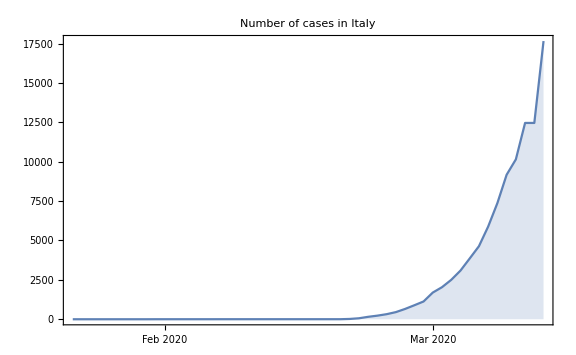

```mathematica
DateListPlot[{italyConfirmedCasesTS},PlotRange->All,Filling->Axis,PlotLabel->"Number of cases in Italy",PlotRange->All,ImageSize->Large]
```

We can also look at the number of recoveries confirmed.

```mathematica
italyRecoveredCasesTS=italyEpi⟦All,"RecoveredCases"⟧
```

Dataset[<>]

Let’s plot both these timeseries.

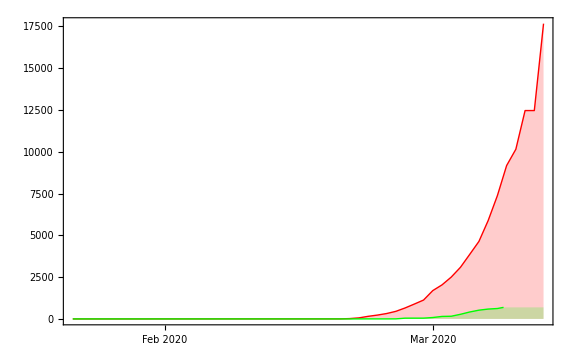

```mathematica
Show[DateListPlot[italyConfirmedCasesTS,PlotRange->All,PlotStyle->{Red,Thick},Filling->Axis,ImageSize->Large],DateListPlot[italyRecoveredCasesTS,PlotStyle->{Green,Thick},Filling->Axis]]
```

To extract the numerical values captured for every day in the timeseries object, we need to apply the List function to it

```mathematica
Apply[List,italyConfirmedCasesTS,{1}](*Applying the List function only to level 1*)
```

Dataset[<>]

Note, we could also have used the shorthand notation List@@@italyConfirmedCasesTS.  Using the Normal function, we can extract a nested list with datetime objects and the actual values.

```mathematica
Normal[List@@@italyConfirmedCasesTS⟦1⟧]
```

{{Wed 22 Jan 2020 00:00:00GMT+2.,0},{Thu 23 Jan 2020 00:00:00GMT+2.,0},{Fri 24 Jan 2020 00:00:00GMT+2.,0},{Sat 25 Jan 2020 00:00:00GMT+2.,0},{Sun 26 Jan 2020 00:00:00GMT+2.,0},{Mon 27 Jan 2020 00:00:00GMT+2.,0},{Tue 28 Jan 2020 00:00:00GMT+2.,0},{Wed 29 Jan 2020 00:00:00GMT+2.,0},{Thu 30 Jan 2020 00:00:00GMT+2.,0},{Fri 31 Jan 2020 00:00:00GMT+2.,2},{Sat 1 Feb 2020 00:00:00GMT+2.,2},{Sun 2 Feb 2020 00:00:00GMT+2.,2},{Mon 3 Feb 2020 00:00:00GMT+2.,2},{Tue 4 Feb 2020 00:00:00GMT+2.,2},{Wed 5 Feb 2020 00:00:00GMT+2.,2},{Thu 6 Feb 2020 00:00:00GMT+2.,2},{Fri 7 Feb 2020 00:00:00GMT+2.,3},{Sat 8 Feb 2020 00:00:00GMT+2.,3},{Sun 9 Feb 2020 00:00:00GMT+2.,3},{Mon 10 Feb 2020 00:00:00GMT+2.,3},{Tue 11 Feb 2020 00:00:00GMT+2.,3},{Wed 12 Feb 2020 00:00:00GMT+2.,3},{Thu 13 Feb 2020 00:00:00GMT+2.,3},{Fri 14 Feb 2020 00:00:00GMT+2.,3},{Sat 15 Feb 2020 00:00:00GMT+2.,3},{Sun 16 Feb 2020 00:00:00GMT+2.,3},{Mon 17 Feb 2020 00:00:00GMT+2.,3},{Tue 18 Feb 2020 00:00:00GMT+2.,3},{Wed 19 Feb 2020 00:00:00GMT+2.,3},{Thu 20 Feb 2020 00:00:00GMT+2.,3},{Fri 21 Feb 2020 00:00:00GMT+2.,20},{Sat 22 Feb 2020 00:00:00GMT+2.,62},{Sun 23 Feb 2020 00:00:00GMT+2.,155},{Mon 24 Feb 2020 00:00:00GMT+2.,229},{Tue 25 Feb 2020 00:00:00GMT+2.,322},{Wed 26 Feb 2020 00:00:00GMT+2.,453},{Thu 27 Feb 2020 00:00:00GMT+2.,655},{Fri 28 Feb 2020 00:00:00GMT+2.,888},{Sat 29 Feb 2020 00:00:00GMT+2.,1128},{Sun 1 Mar 2020 00:00:00GMT+2.,1694},{Mon 2 Mar 2020 00:00:00GMT+2.,2036},{Tue 3 Mar 2020 00:00:00GMT+2.,2502},{Wed 4 Mar 2020 00:00:00GMT+2.,3089},{Thu 5 Mar 2020 00:00:00GMT+2.,3858},{Fri 6 Mar 2020 00:00:00GMT+2.,4636},{Sat 7 Mar 2020 00:00:00GMT+2.,5883},{Sun 8 Mar 2020 00:00:00GMT+2.,7375},{Mon 9 Mar 2020 00:00:00GMT+2.,9172},{Tue 10 Mar 2020 00:00:00GMT+2.,10149},{Wed 11 Mar 2020 00:00:00GMT+2.,12462},{Thu 12 Mar 2020 00:00:00GMT+2.,12462},{Fri 13 Mar 2020 00:00:00GMT+2.,17660}}

Since we only need the values, we can use indexing to extract all the second elements in each nested list.

```mathematica
tsmItaly=TimeSeriesModelFit[Normal[List@@@italyConfirmedCasesTS⟦1⟧]⟦All,2⟧]
```

TimeSeriesModel[…]

TimeSeriesModel[…]

There are various properties and information that is available for the model.

```mathematica
tsmItaly["Properties"]
```

{ACFPlot,ACFValues,AIC,AICc,BIC,BestFit,BestFitParameters,CandidateModels,CandidateModelSelectionValues,CandidateSelectionTable,CandidateSelectionTableEntries,CovarianceMatrix,ErrorVariance,FitResiduals,ForecastStandardErrors,InformationMatrix,LjungBoxPlot,LjungBoxValues,ModelFamily,PACFPlot,PACFValues,ParameterConfidenceIntervals,ParameterTable,ParameterTableEntries,PredictionLimits,Properties,SBC,SelectionCriterion,StandardizedResiduals,TemporalData}

```mathematica
Normal[tsmItaly](*Information on the time series model*)
```

SARIMAProcess[982.529,{},1,{},{17,{},2,{}},1.37118×10^6]

We can now create a plot that shows the prediction 10 days into the future.

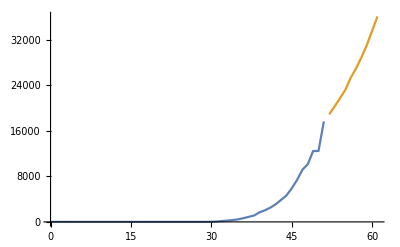

```mathematica
ListLinePlot[{tsmItaly["TemporalData"],TimeSeriesForecast[tsmItaly,{10}]}]
```

The first row in the dataset is of Hubei, where the number of cases have reached a plateau.  Let’s model the next 10 days there as well.

```mathematica
hubeiConfirmedCasesTS=epiData⟦1,"ConfirmedCases"⟧
```

TimeSeries[…]

```mathematica
hubeiConfirmedCasesValues=Flatten[List@@@hubeiConfirmedCasesTS⟦2⟧⟦1⟧]
```

{444,444,549,761,1058,1423,3554,3554,4903,5806,7153,11177,13522,16678,19665,22112,24953,27100,29631,31728,33366,33366,48206,54406,56249,58182,59989,61682,62031,62442,62662,64084,64084,64287,64786,65187,65596,65914,66337,66907,67103,67217,67332,67466,67592,67666,67707,67743,67760,67773,67781,67786}

```mathematica
tsmHubei=TimeSeriesModelFit[hubeiConfirmedCasesValues,"SARIMA"]
```

TimeSeriesModel[…]

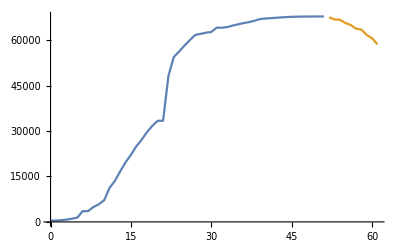

```mathematica
ListLinePlot[{tsmHubei["TemporalData"],TimeSeriesForecast[tsmHubei,{10}]}]
```

As a last contrast, let’s look at the United Kingdom.

```mathematica
uk=Interpreter["Country"]["United Kingdom"]
```

United Kingdom

```mathematica
ukEpi=epiData[Select[MatchQ[#Country,uk]&]]
```

Dataset[<>]

```mathematica
ukConfirmedCasesTS=ukEpi⟦1,"ConfirmedCases"⟧;
```

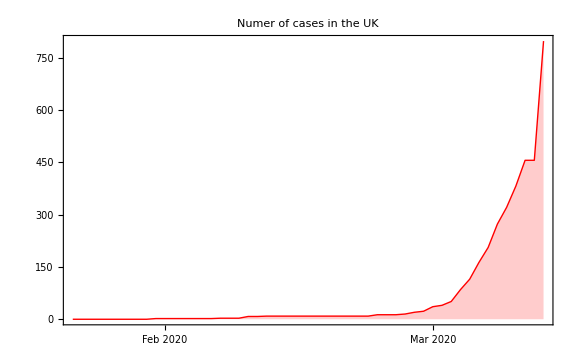

```mathematica
DateListPlot[ukConfirmedCasesTS,PlotLabel->"Numer of cases in the UK",PlotRange->All,PlotStyle->{Red,Thick},Filling->Axis,ImageSize->Large]
```

```mathematica
tsmUK=TimeSeriesModelFit[Normal[List@@@ukConfirmedCasesTS]⟦All,2⟧,"SARIMA"]
```

TimeSeriesModel[…]

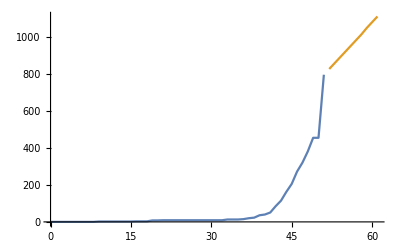

```mathematica
ListLinePlot[{tsmUK["TemporalData"],TimeSeriesForecast[tsmUK,{10}]}]
```

For many countries like China and Australia, we have data broken down into various regions, territories, and provinces.

```mathematica
australia=Entity["Country","Australia"]
```

Australia

```mathematica
australiaAllEpi=epiData[Select[MatchQ[#Country,australia]&]]
```

Dataset[<>]

Now we can plot the seven listed administrative divisions.  The DateListPlot function can take timeseries objects and legends as arguments.

```mathematica
Legended[#⟦4⟧,#⟦1⟧]&/@australiaAllEpi⟦;;7⟧(*Click on any of the seven entries*)
```

Dataset[<>]

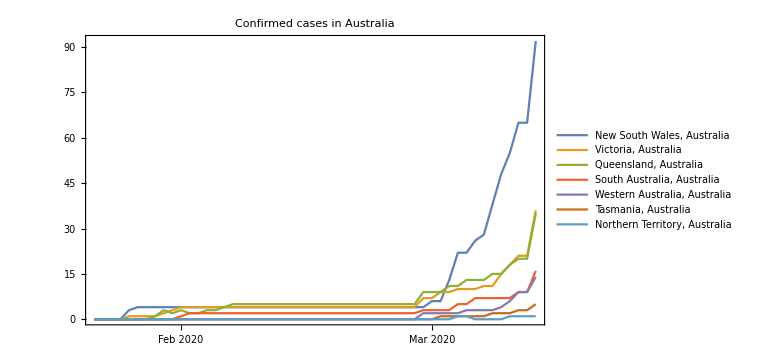

```mathematica
DateListPlot[Legended[#⟦4⟧,#⟦1⟧]&/@australiaAllEpi⟦;;7⟧,PlotLabel->"Confirmed cases in Australia",PlotRange->All,ImageSize->Large]
```

## Countries with most confirmed cases

We can get a list of all the countries by using DeleteDuplicates.

```mathematica
countriesAffected=Sort[DeleteDuplicates[DeleteMissing[Normal[epiData[All,"Country"]]]]]
```

{Afghanistan,Albania,Algeria,Andorra,Antigua and Barbuda,Argentina,Armenia,Aruba,Australia,Austria,Azerbaijan,Bahrain,Bangladesh,Belarus,Belgium,Bhutan,Bolivia,Bosnia and Herzegovina,Brazil,Brunei,Bulgaria,Burkina Faso,Cambodia,Cameroon,Canada,Cayman Islands,Chile,China,Colombia,Costa Rica,Croatia,Cuba,Cyprus,Czech Republic,Democratic Republic of the Congo,Denmark,Dominican Republic,Ecuador,Egypt,Estonia,Ethiopia,Finland,France,French Guiana,Georgia,Germany,Greece,Guadeloupe,Guinea,Guyana,Honduras,Hong Kong,Hungary,Iceland,India,Indonesia,Iran,Iraq,Ireland,Israel,Italy,Ivory Coast,Jamaica,Japan,Jordan,Kazakhstan,Kenya,Kuwait,Latvia,Lebanon,Liechtenstein,Lithuania,Luxembourg,Macau,North Macedonia,Malaysia,Maldives,Malta,Martinique,Mexico,Moldova,Monaco,Mongolia,Morocco,Nepal,Netherlands,New Zealand,Nigeria,Norway,Oman,Pakistan,Panama,Paraguay,Peru,Philippines,Poland,Portugal,Qatar,Réunion,Romania,Russia,San Marino,Saudi Arabia,Senegal,Serbia,Singapore,Slovakia,Slovenia,South Africa,South Korea,Spain,Sri Lanka,Sudan,Sweden,Switzerland,Taiwan,Thailand,Togo,Tunisia,Turkey,Ukraine,United Arab Emirates,United Kingdom,United States,Vatican City,Vietnam}

Let’s see a world map of all cases in the dataset.

```mathematica
GeoGraphics[{GeoMarker[DeleteMissing[Normal[epiData[All,#GeoPosition&]]]]},ImageSize->Large]
```

-Graphics-

The ConfirmedCases column is a timeseries object in itself.  We can extract the “LastValue” from this time series to get the total number of values.  Our first aim is to create a dataset object with sum totals of the country counts (remembering that some countries have their data broken up into regions), so we will use the GroupBy function and the Total Function of all the “LastValue” values.

```mathematica
epiData[GroupBy["Country"],Total,#ConfirmedCases["LastValue"]&]
```

Dataset[<>]

A GeoRegionValuePlot will give a better indication of the relative number of cases per country.

```mathematica
GeoRegionValuePlot[epiData[GroupBy["Country"],Total,#ConfirmedCases["LastValue"]&],PlotRange->5000,ImageSize->Large]
```

-Graphics-

We can do the same plotting for a specific country (with individual administrative divisions).  Below, we look at the United States.

```mathematica
usa=Interpreter["Country"]["United States"]
```

United States

```mathematica
usaEpiData=Select[epiData,#Country==usa&]
```

Dataset[<>]

```mathematica
GeoRegionValuePlot[usaEpiData[GroupBy["AdministrativeDivision"],Total,#ConfirmedCases["LastValue"]&],PlotRange->100,ImageSize->Large]
```

-Graphics-

We want to sort the country numbers in descending order and only list the top 10 countries.  Note that one value will not be a country (at the time of this recording) as it contains values for a ship.  Therefor, we will list the top 11 and later delete this entry.

```mathematica
top10Countries=Sort[epiData[GroupBy["Country"],Total,#ConfirmedCases["LastValue"]&]⟦;;11⟧,Greater]
```

Dataset[<>]

We can convert this dataset object to an association using the Normal function.  Note the NotACountryCruiseShip entry (at the time of this recording).

```mathematica
top10CountriesAssociation=Normal[top10Countries]
```

<|China→80801,Italy→17660,Iran→11364,South Korea→7979,Spain→5232,Germany→3675,France→3667,Switzerland→1139,Norway→996,Sweden→814,Netherlands→804|>

The KeyDrop function will allow us to delete the mentioned entry.

```mathematica
top10CountriesAssociation=KeyDrop[top10CountriesAssociation,Missing["NotACountryCruiseShip"]]
```

<|China→80801,Italy→17660,Iran→11364,South Korea→7979,Spain→5232,Germany→3675,France→3667,Switzerland→1139,Norway→996,Sweden→814,Netherlands→804|>

Now we can create a bar chart of the data.

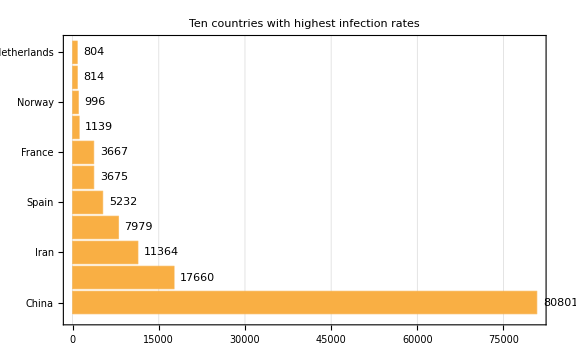

```mathematica
BarChart[top10CountriesAssociation,ChartLabels->Automatic,BarOrigin->Left,LabelingFunction->After,PlotLabel->"Ten countries with highest infection rates",PlotTheme->"Business",ImageSize->Large]
```

We can also create a bar chart with legends.  First we extract the country names.

```mathematica
Keys@top10CountriesAssociation
```

{China,Italy,Iran,South Korea,Spain,Germany,France,Switzerland,Norway,Sweden,Netherlands}

Now we convert them to names.

```mathematica
top10CountryNames=EntityValue[Keys[top10CountriesAssociation],"Name"]
```

{China,Italy,Iran,South Korea,Spain,Germany,France,Switzerland,Norway,Sweden,Netherlands}

We also need to extract the counts.

```mathematica
top10CountriesTotal=Values@top10CountriesAssociation
```

{80801,17660,11364,7979,5232,3675,3667,1139,996,814,804}

Now we can create the required bar chart.

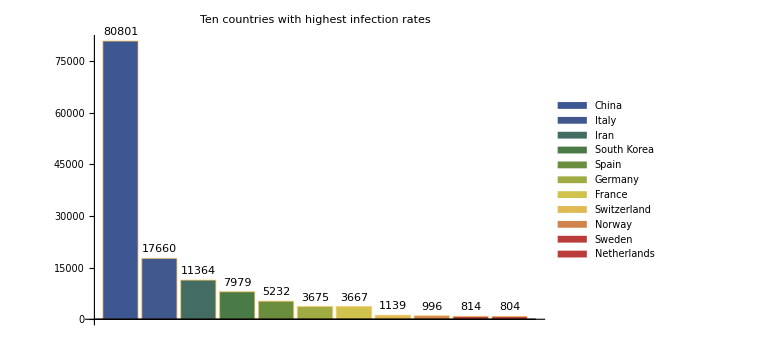

```mathematica
BarChart[top10CountriesTotal,ChartLegends->top10CountryNames,PlotLabel->"Ten countries with highest infection rates",ChartStyle->"DarkRainbow",LabelingFunction->Above,ImageSize->Large]
```